```mathematica
a = 0.5;
b = 0.3;
c = 0.5;
d = 0.5;
e = 0.1;
k = 0.7;
K = 500;
m = 0.5;
rt = 100;
sol=NDSolve[{s'[t]== m*s[t]*(1-s[t]/K)-a*s[t]*z[t]+k*z[t],
i'[t]==a*s[t]*z[t]-d*i[t]-e*i[t],
z'[t]==-k*z[t]+d*i[t]-b*s[t]*z[t]+c*r[t],
r'[t]==b*s[t]*z[t]+e*i[t]-c*r[t],
i[0]==r[0]==0, s[0]==500, z[0] == 1},{s,i,z,r},{t,0, rt}]
```

{{s→InterpolatingFunction[…],i→InterpolatingFunction[…],z→InterpolatingFunction[…],r→InterpolatingFunction[…]}}

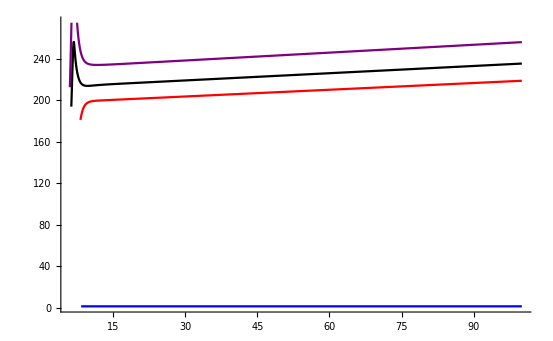

```mathematica
splot = Plot[Evaluate[{s[t]}  /. sol], {t, 0, rt}, PlotStyle->Blue];
zplot = Plot[Evaluate[{z[t]}  /. sol], {t, 0, rt}, PlotStyle->Red];
iplot = Plot[Evaluate[{i[t]}  /. sol], {t, 0, rt}, PlotStyle->Purple];
rplot = Plot[Evaluate[{r[t]}  /. sol], {t, 0, rt}, PlotStyle->Black];
Show[splot, zplot, iplot, rplot, PlotRange->All]
```